# Woods-Saxon Potential

## Micah Buuck

6/17/13

## Constants and Initial Conditions

Originally I tried to make use of Mathematica's built-in unit handling, but I couldn't figure out how to make that work with plotting, so I gave up. I left the code for it in, but commented it out.

```mathematica
(*<<Units`
Needs["PhysicalConstants`"]*)
Needs["PlotLegends`"]
```

```mathematica
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
R=3 (*Femto Meter*);
V0=(-1.9-.38*I)*ℏc^2/(2*m) (*Mega ElectronVolt*);
a=.54 (*Femto Meter*);
V[r_]:=V0/(1+E^((r-R)/a));
```

### Plot for potential

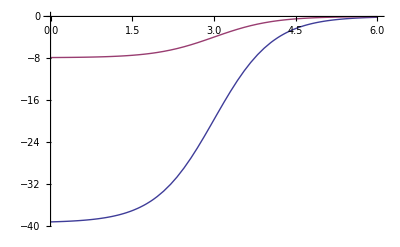

```mathematica
Plot[{Re[V[r]],Im[V[r]]},{r,0,2*R}]
```

## Solve the Schrödinger Equation

First I solve the Schrödinger equation for the radial wavefunction with an arbitrary constant for the initial condition for u'(0). My goal is to show that the resulting phase shift we get from this in independent of the choice of u'(0).

```mathematica
s[L_,k_,b_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==b},u,{r,(1000*k)^(-1),5*R}]
```

```mathematica
u[L_,k_,r_,b_]:=u[r]/.s[L,k,b][[1]]
```

```mathematica
β[L_,k_,b_]:=5*R/Evaluate[u[L,k,5*R,b]]*(D[u[L,k,r,b],r]/.r->(5*R))-1
tanδ[L_,k_,b_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k,b]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k,b]*SphericalBesselY[L,k*5*R])]
```

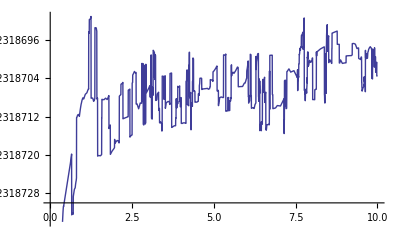

```mathematica
Plot[Re[tanδ[0,1,b]],{b,0.01,10}]
```

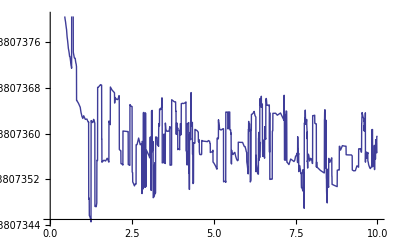

```mathematica
Plot[Im[tanδ[0,1,b]],{b,0.01,10}]
```

As we can see from this plot of tanδ vs. u'(0), the phase shift appears to be independent of our choice of u'(0) up to about 0.01% error.

## Reformulate tanδ for specific choice of u'(0)

These are the same equations as above, but now we have chosen u'(0)=8 (an arbitrary choice).

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
β[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k]*SphericalBesselY[L,k*5*R])]
```

```mathematica
Table[tanδ[L,1],{L,0,20}]
```

{-0.923187+0.738074 ⅈ,-1.22237+1.20904 ⅈ,-1.58735+1.99802 ⅈ,1.00564+1.1644 ⅈ,0.211335+0.0713622 ⅈ,0.0403135+0.00963108 ⅈ,0.00812726+0.00172725 ⅈ,0.00165119+0.000337094 ⅈ,0.000333925+0.0000672485 ⅈ,0.0000671337+0.0000134576 ⅈ,0.0000134081+2.6876×10^-6 ⅈ,2.6722×10^-6+5.35051×10^-7 ⅈ,5.30794×10^-7+1.06139×10^-7 ⅈ,1.05238×10^-7+2.09407×10^-8 ⅈ,2.36222×10^-8+4.08615×10^-9 ⅈ,6.62046×10^-9+7.80279×10^-10 ⅈ,1.01519×10^-9+1.43713×10^-10 ⅈ,1.04656×10^-10+2.51393×10^-11 ⅈ,-3.4111×10^-12+4.1209×10^-12 ⅈ,-3.93433×10^-12+6.26806×10^-13 ⅈ,-1.06641×10^-13+8.79197×10^-14 ⅈ}

For k=1, tanδ becomes negligible after about L=5. This is also evident in the plot for continuous L below.

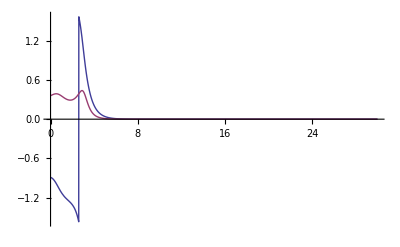

```mathematica
Plot[{Re[ArcTan[tanδ[L,1]]],Im[ArcTan[tanδ[L,1]]]},{L,0,30},PlotRange->{-Pi/2,Pi/2}]
```

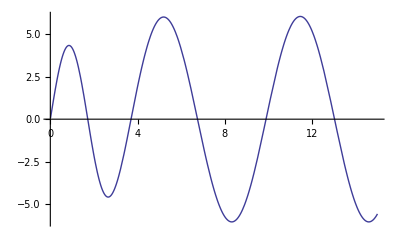

```mathematica
Plot[Evaluate[u[0,1,r]],{r,(100)^(-1),5*R}]
```

Plugging this phase shift into the equations for the scattering amplitude is:

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,2*k*R}]
```

Here is a table of some values of dσ/dΩ as a function of θ.

```mathematica
Clear[dσdΩ]
```

```mathematica
dσdΩ[k_]:=Table[{θ,Abs[f[k,θ]]^2},{θ,0,Pi,.1}]
```

```mathematica
dσdΩ[1]
```

```mathematica
{{0.,138.24735648211183},{0.1,131.96418694419444},{0.2,114.6592654903783},{0.30000000000000004,90.39468602293465},{0.4,64.30834749550795},{0.5,40.96502717809941},{0.6000000000000001,23.185107373198356},{0.7000000000000001,11.715122859819573},{0.8,5.663523548401128},{0.9,3.3198513944892047},{1.,2.9319238824176685},{1.1,3.1817325211565817},{1.2000000000000002,3.323652386316457},{1.3,3.0953167489705633},{1.4000000000000001,2.5414915172058445},{1.5,1.8454757211071333},{1.6,1.2047526866685199},{1.7000000000000002,0.7547245075757844},{1.8,0.53626863531564},{1.9000000000000001,0.5023777111949094},{2.,0.5545725801561825},{2.1,0.5922118641706786},{2.2,0.5545270708340819},{2.3000000000000003,0.44029499749236833},{2.4000000000000004,0.3009951398837256},{2.5,0.21397933778536093},{2.6,0.2479553016653255},{2.7,0.43331787347604256},{2.8000000000000003,0.7467074651808787},{2.9000000000000004,1.1146726795353727},{3.,1.4359192277790755},{3.1,1.6154058368157207}}
```

{{0.,138.247},{0.1,131.964},{0.2,114.659},{0.3,90.3947},{0.4,64.3083},{0.5,40.965},{0.6,23.1851},{0.7,11.7151},{0.8,5.66352},{0.9,3.31985},{1.,2.93192},{1.1,3.18173},{1.2,3.32365},{1.3,3.09532},{1.4,2.54149},{1.5,1.84548},{1.6,1.20475},{1.7,0.754725},{1.8,0.536269},{1.9,0.502378},{2.,0.554573},{2.1,0.592212},{2.2,0.554527},{2.3,0.440295},{2.4,0.300995},{2.5,0.213979},{2.6,0.247955},{2.7,0.433318},{2.8,0.746707},{2.9,1.11467},{3.,1.43592},{3.1,1.61541}}

```mathematica
interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

Here is a log plot of that same information.

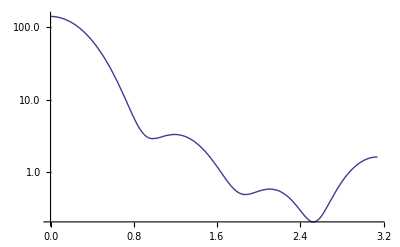

```mathematica
p1=LogPlot[interp1[θ],{θ,0,Pi}]
```

## Eikonal Approximation

These equations come straight out of Sakurai, equations 7.4.13 and 7.4.14 (page 394).

```mathematica
χ0[k_,b_]=-2*m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,15}];
T0[k_,b_]:=Exp[I*χ0[k,b]]-1
Eif0[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T0[k,b],{b,0,15}]
```

I had to have the iteration of the table below happen in integer steps because doing it in decimal steps was giving Mathematica problems somehow. I think it probably has something to do with differences in the way it handles integers and floats.

```mathematica
eik0dσdΩ[k_]:=Table[{θ/10.,Abs[Eif0[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eik0dσdΩ[1]
```

```mathematica
{{0,77.81449298353003},{0.1,74.35383330732927},{0.2,64.84837991679096},{0.30000000000000004,51.57988020244924},{0.4,37.37770256118771},{0.5,24.684171090312795},{0.6000000000000001,14.948965384363145},{0.7000000000000001,8.51791645462917},{0.8,4.915230121696361},{0.9,3.281874841998521},{1.,2.7553515339408743},{1.1,2.6857105335099236},{1.2000000000000002,2.6902902457515094},{1.3,2.6068136696049393},{1.4000000000000001,2.4104679946468877},{1.5,2.1388434537513845},{1.6,1.8425250325094127},{1.7000000000000002,1.5611567627514344},{1.8,1.3170427344045403},{1.9000000000000001,1.1176866720757859},{2.,0.9611434858445198},{2.1,0.8409452369136389},{2.2,0.7494715126304502},{2.3000000000000003,0.6797742195028705},{2.4000000000000004,0.6262920150255549},{2.5,0.5849232679639141},{2.6,0.5528078924322809},{2.7,0.5280292166366286},{2.8000000000000003,0.5093396281148677},{2.9000000000000004,0.4959471492852086},{3.,0.48736597027500483},{3.1,0.48332051398465925}}
```

{{0,77.8145},{0.1,74.3538},{0.2,64.8484},{0.3,51.5799},{0.4,37.3777},{0.5,24.6842},{0.6,14.949},{0.7,8.51792},{0.8,4.91523},{0.9,3.28187},{1.,2.75535},{1.1,2.68571},{1.2,2.69029},{1.3,2.60681},{1.4,2.41047},{1.5,2.13884},{1.6,1.84253},{1.7,1.56116},{1.8,1.31704},{1.9,1.11769},{2.,0.961143},{2.1,0.840945},{2.2,0.749472},{2.3,0.679774},{2.4,0.626292},{2.5,0.584923},{2.6,0.552808},{2.7,0.528029},{2.8,0.50934},{2.9,0.495947},{3.,0.487366},{3.1,0.483321}}

```mathematica
eik0interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

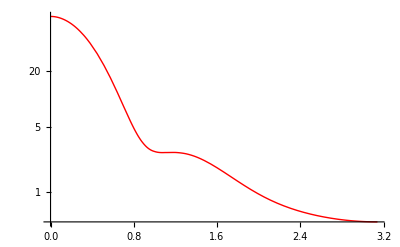

```mathematica
eik0p1=LogPlot[eik0interp1[θ],{θ,0,Pi},PlotStyle->Red]
```

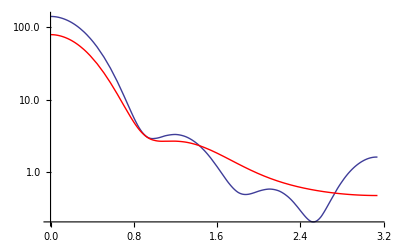

```mathematica
Show[p1,eik0p1]
```

As you can see above, the two plots actually agree with each other pretty well, especially at small θ. There is some pretty obvious disagreement for large θ, however, and the eikonal approximation seems to miss some of the structure apparent in the partial wave formulation.

## Check Method for k=10

For k=10, then k^2 = 100 >> 2*m*V/ℏ^2 ~= -2 - 0.4i, so the eikonal approximation should be valid.

```mathematica
dσdΩ[10]//Timing
```

{510.822,{{0.,486.366},{0.1,13.7655},{0.2,0.142722},{0.3,0.00212583},{0.4,0.000122783},{0.5,1.06992×10^-6},{0.6,3.82125×10^-6},{0.7,1.5606×10^-6},{0.8,9.09828×10^-7},{0.9,4.56746×10^-7},{1.,2.06863×10^-7},{1.1,7.29154×10^-8},{1.2,1.35146×10^-8},{1.3,1.44845×10^-9},{1.4,1.86539×10^-8},{1.5,5.22517×10^-8},{1.6,9.36151×10^-8},{1.7,1.35377×10^-7},{1.8,1.73879×10^-7},{1.9,2.03822×10^-7},{2.,2.24481×10^-7},{2.1,2.3388×10^-7},{2.2,2.31779×10^-7},{2.3,2.17965×10^-7},{2.4,1.94183×10^-7},{2.5,1.61737×10^-7},{2.6,1.23014×10^-7},{2.7,8.11484×10^-8},{2.8,4.02909×10^-8},{2.9,8.73381×10^-9},{3.,6.19344×10^-9},{3.1,1.49821×10^-7}}}

The first number above is the time that command took to evaluate.

```mathematica
interp10=Interpolation[%[[2]]];
```

InterpolatingFunction[{{0.,3.1}},<>]

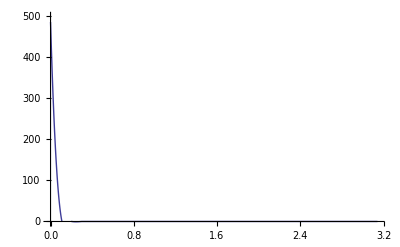

```mathematica
p10=Plot[interp10[θ],{θ,0,Pi},PlotRange->{-1,500}]
```

```mathematica
eik0dσdΩ[10]//Timing
```

{225.703,{{0,486.162},{0.1,14.0605},{0.2,0.13689},{0.3,0.00246745},{0.4,0.0000540022},{0.5,1.42675×10^-6},{0.6,3.23853×10^-8},{0.7,1.29725×10^-9},{0.8,5.91253×10^-11},{0.9,1.26869×10^-11},{1.,8.34575×10^-12},{1.1,3.54278×10^-12},{1.2,2.08122×10^-12},{1.3,1.19259×10^-12},{1.4,7.31612×10^-13},{1.5,4.70504×10^-13},{1.6,3.14678×10^-13},{1.7,2.18652×10^-13},{1.8,1.57428×10^-13},{1.9,1.16839×10^-13},{2.,8.94036×10^-14},{2.1,7.03232×10^-14},{2.2,5.67563×10^-14},{2.3,4.69704×10^-14},{2.4,3.98201×10^-14},{2.5,3.45317×10^-14},{2.6,3.05815×10^-14},{2.7,2.77058×10^-14},{2.8,2.55993×10^-14},{2.9,2.41731×10^-14},{3.,2.32565×10^-14},{3.1,2.28285×10^-14}}}

You can see that as k increases, the eikonal approximation evaluates faster than the partial wave expansion, as we would expect.

```mathematica
eik0interp10=Interpolation[%[[2]]];
```

InterpolatingFunction[{{0.,3.1}},<>]

The points we evaluated dσ/dΩ at are not dense enough to really capture all the detail at small θ, so that's why the plots for k = 10 aren't very good. A better interpolation could be made, but it would take some time.

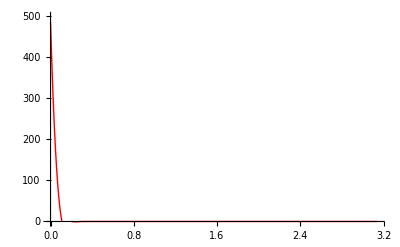

```mathematica
eik0p10=Plot[eik0interp10[θ],{θ,0,Pi},PlotRange->{-1,500},PlotStyle->Red]
```

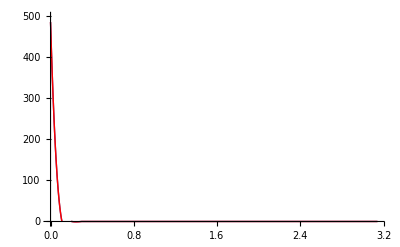

```mathematica
Show[p10,eik0p10]
```

## Plots for k=1,2,3

```mathematica
dσdΩ[2]
```

{{0.,294.133},{0.1,254.454},{0.2,163.583},{0.3,76.4455},{0.4,25.1958},{0.5,6.35473},{0.6,2.53503},{0.7,2.01532},{0.8,1.36054},{0.9,0.647556},{1.,0.246628},{1.1,0.124859},{1.2,0.0972809},{1.3,0.0693531},{1.4,0.0399179},{1.5,0.0199396},{1.6,0.00965119},{1.7,0.00640806},{1.8,0.00574316},{1.9,0.00435876},{2.,0.00275605},{2.1,0.00182001},{2.2,0.00102615},{2.3,0.000486702},{2.4,0.000452967},{2.5,0.000407829},{2.6,0.000224844},{2.7,0.000165988},{2.8,0.000223775},{2.9,0.000166481},{3.,0.000245865},{3.1,0.000613277}}

```mathematica
interp2=Interpolation[%];
```

```mathematica
eik0dσdΩ[2]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,251.192},{0.1,218.078},{0.2,142.436},{0.3,69.6934},{0.4,25.7959},{0.5,8.17661},{0.6,3.44878},{0.7,2.25907},{0.8,1.46341},{0.9,0.785982},{1.,0.37341},{1.1,0.186334},{1.2,0.110689},{1.3,0.0727448},{1.4,0.0468667},{1.5,0.028506},{1.6,0.0168265},{1.7,0.0101767},{1.8,0.00658463},{1.9,0.00457904},{2.,0.0033391},{2.1,0.00248921},{2.2,0.00187436},{2.3,0.00142542},{2.4,0.00110132},{2.5,0.000870884},{2.6,0.000709192},{2.7,0.000597083},{2.8,0.00052068},{2.9,0.000470474},{3.,0.000440333},{3.1,0.000426674}}

```mathematica
eik0interp2=Interpolation[%];
```

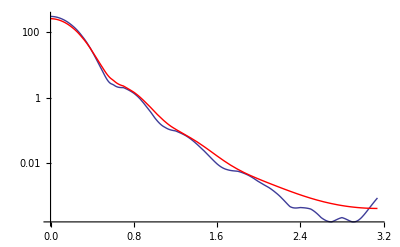

```mathematica
p2=LogPlot[interp2[θ],{θ,0,Pi}];
eik0p2=LogPlot[eik0interp2[θ],{θ,0,Pi},PlotStyle->Red];
Show[p2,eik0p2]
```

```mathematica
dσdΩ[3]
```

{{0.,372.486},{0.1,274.217},{0.2,105.81},{0.3,19.0402},{0.4,2.01384},{0.5,1.18455},{0.6,0.5426},{0.7,0.107501},{0.8,0.0414711},{0.9,0.0251555},{1.,0.00805638},{1.1,0.00217301},{1.2,0.00131856},{1.3,0.0009061},{1.4,0.000261088},{1.5,0.000134707},{1.6,0.0000310148},{1.7,0.0000296531},{1.8,0.000010833},{1.9,0.0000113171},{2.,8.71355×10^-6},{2.1,7.9032×10^-6},{2.2,1.10716×10^-6},{2.3,3.59257×10^-6},{2.4,3.71053×10^-6},{2.5,1.46767×10^-6},{2.6,9.20486×10^-6},{2.7,3.64465×10^-7},{2.8,8.93753×10^-6},{2.9,0.000010317},{3.,2.50062×10^-6},{3.1,0.0000885575}}

```mathematica
interp3=Interpolation[%];
```

```mathematica
eik0dσdΩ[3]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,349.768},{0.1,258.357},{0.2,102.291},{0.3,20.4603},{0.4,2.64687},{0.5,1.17683},{0.6,0.54204},{0.7,0.137557},{0.8,0.0419746},{0.9,0.0217471},{1.,0.00879354},{1.1,0.0028291},{1.2,0.00117665},{1.3,0.000612173},{1.4,0.000279359},{1.5,0.000113006},{1.6,0.00005089},{1.7,0.0000278296},{1.8,0.0000158796},{1.9,8.6199×10^-6},{2.,4.58679×10^-6},{2.1,2.58299×10^-6},{2.2,1.61136×10^-6},{2.3,1.09628×10^-6},{2.4,7.83163×10^-7},{2.5,5.74738×10^-7},{2.6,4.32226×10^-7},{2.7,3.35564×10^-7},{2.8,2.71491×10^-7},{2.9,2.30668×10^-7},{3.,2.0683×10^-7},{3.1,1.96228×10^-7}}

```mathematica
eik0interp3=Interpolation[%];
```

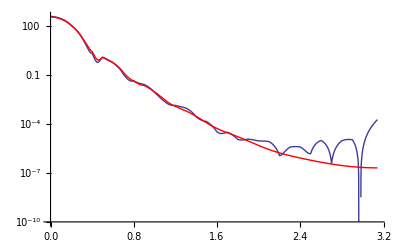

```mathematica
p3=LogPlot[interp3[θ],{θ,0,Pi}];
eik0p3=LogPlot[eik0interp3[θ],{θ,0,Pi},PlotStyle->Red];
Show[p3,eik0p3]
```

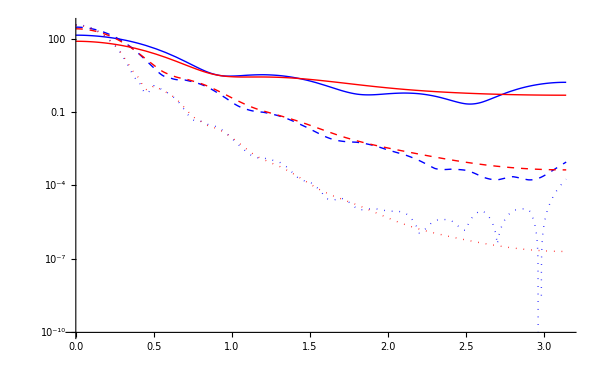

```mathematica
LogPlot[{interp1[θ],eik0interp1[θ],interp2[θ],eik0interp2[θ],interp3[θ],eik0interp3[θ]},{θ,0,Pi},PlotStyle->{{Blue},{Red},{Blue,Dashed},{Red,Dashed},{Blue,Dotted},{Red,Dotted}},PlotLegend->{"Partial Wave: k=1","Eikonal: k=1","Partial Wave: k=2","Eikonal: k=2","Partial Wave: k=3","Eikonal: k=3"},LegendPosition->{1.1,-0.4},LegendSize->{1,1},ImageSize->600]
```

The eikonal approximation actually appears to track the partial wave expansion quite well for k = 1, 2, and 3, but is again missing a lot of the finer structure.

## Plot for k=0.1

As you can see below, the approximation gets pretty bad as k -> 0.

```mathematica
Abs[f[.1,0]]^2
```

9.73572

```mathematica
Abs[Eif0[.1,0]]^2
```

2.19448

```mathematica
interp01=Interpolation[dσdΩ[.1]];
eik0interp01=Interpolation[eik0dσdΩ[.1]];
```

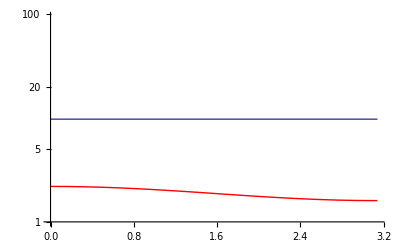

```mathematica
p01=LogPlot[interp01[θ],{θ,0,Pi}];
eik0p01=LogPlot[eik0interp01[θ],{θ,0,Pi},PlotStyle->Red];
Show[p01,eik0p01]
```

## Add in Eikonal Corrections

### First order correction

```mathematica
En[k_]:=(k*ℏc)^2/(2*m)
U[r_]:=V[r]/V0
ϵ[k_]:=V0/(2*En[k])
```

```mathematica
τ1[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+b*D[#,b])&[U[Sqrt[z^2+b^2]]^2]],{z,0,15}];
```

```mathematica
T1[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b])]-1
Eif1[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T1[k,b],{b,0,15}]
```

```mathematica
eik1dσdΩ[k_]:=Table[{θ/10.,Abs[Eif1[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eik1dσdΩ[1]
```

{{0,95.4916},{0.1,91.322},{0.2,79.8603},{0.3,63.8325},{0.4,46.6181},{0.5,31.1322},{0.6,19.1034},{0.7,10.9457},{0.8,6.10314},{0.9,3.58056},{1.,2.39601},{1.1,1.82978},{1.2,1.47535},{1.3,1.1702},{1.4,0.890037},{1.5,0.660611},{1.6,0.506438},{1.7,0.432378},{1.8,0.425104},{1.9,0.462055},{2.,0.520177},{2.1,0.581276},{2.2,0.633878},{2.3,0.672689},{2.4,0.696956},{2.5,0.708656},{2.6,0.711005},{2.7,0.707442},{2.8,0.701046},{2.9,0.694284},{3.,0.688937},{3.1,0.686134}}

```mathematica
eik1interp1=Interpolation[%];
```

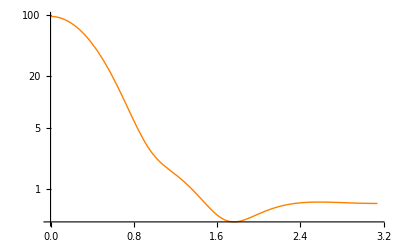

```mathematica
eik1p1=LogPlot[eik1interp1[θ],{θ,0,Pi},PlotStyle->Orange]
```

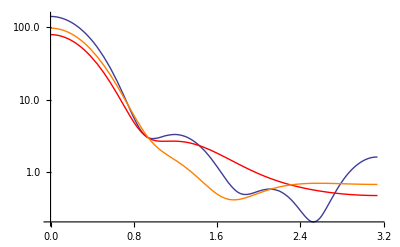

```mathematica
Show[p1,eik0p1,eik1p1]
```

### Second order correction

```mathematica
τ2[k_,b_]=-k*ϵ[k]^3*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[U[Sqrt[z^2+b^2]]^3]],{z,0,15}]-b*D[χ0[k,b],b]^3/(24*k^2);
ω2[k_,b_]=D[χ0[k,b],b]*D[b*D[χ0[k,b],b],b]/(8*k^2);
```

```mathematica
T2[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b]+τ2[k,b])]*Exp[-ω2[k,b]]-1
Eif2[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T2[k,b],{b,0,15}]
```

```mathematica
eik2dσdΩ[k_]:=Table[{θ/10.,Abs[Eif2[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eik2dσdΩ[1]
```

{{0,112.031},{0.1,106.896},{0.2,92.7954},{0.3,73.1305},{0.4,52.1158},{0.5,33.3836},{0.6,19.0774},{0.7,9.68851},{0.8,4.48572},{0.9,2.17948},{1.,1.49308},{1.1,1.47992},{1.2,1.59394},{1.3,1.60884},{1.4,1.48934},{1.5,1.28093},{1.6,1.04232},{1.7,0.816281},{1.8,0.624604},{1.9,0.473341},{2.,0.359865},{2.1,0.278148},{2.2,0.221665},{2.3,0.184574},{2.4,0.161982},{2.5,0.149865},{2.6,0.14493},{2.7,0.144507},{2.8,0.146481},{2.9,0.149244},{3.,0.151644},{3.1,0.152952}}

```mathematica
eik2interp1=Interpolation[%];
```

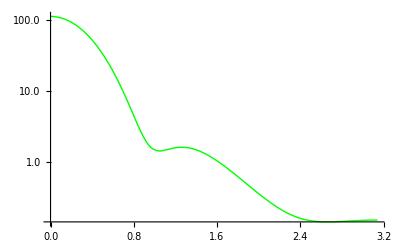

```mathematica
eik2p1=LogPlot[eik2interp1[θ],{θ,0,Pi},PlotStyle->Green]
```

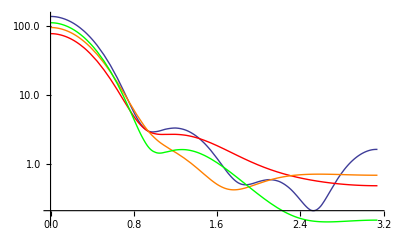

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,PlotRange->Automatic]
```

### Third order correction

```mathematica
τ3[k_,b_]=-k*ϵ[k]^4*NIntegrate[Evaluate[(5/4#+11/4*b*D[#,b]+b^2*D[#,{b,2}]+1/12*b^3*D[#,{b,3}])&[U[Sqrt[z^2+b^2]]^4]],{z,0,15}]-b*D[τ1[k,b],b]*D[χ0[k,b],b]^2/(8*k^2);
ϕ3[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[(1/(2*k)*D[U[Sqrt[z^2+b^2]],b])^2]],{z,0,15}];
ω3[k_,b_]=(D[χ0[k,b],b]*D[b*D[τ1[k,b],b],b]+D[τ1[k,b],b]*D[b*D[χ0[k,b],b],b])/(8*k^2);
```

```mathematica
T3[k_,b_]:=Exp[I*(χ0[k,b]+τ1[k,b]+τ2[k,b]+τ3[k,b]+ϕ3[k,b])]*Exp[-(ω2[k,b]+ω3[k,b])]-1
```

```mathematica
Eif3[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T3[k,b],{b,0,15}]
```

```mathematica
eik3dσdΩ[k_]:=Table[{θ/10.,Abs[Eif3[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eik3dσdΩ[1]
```

{{0,91.4445},{0.1,86.934},{0.2,74.6354},{0.3,57.7358},{0.4,40.1192},{0.5,25.0115},{0.6,14.1374},{0.7,7.6284},{0.8,4.51711},{0.9,3.43732},{1.,3.19103},{1.1,3.02504},{1.2,2.63931},{1.3,2.04368},{1.4,1.3837},{1.5,0.810046},{1.6,0.414108},{1.7,0.217378},{1.8,0.190413},{1.9,0.279713},{2.,0.429794},{2.1,0.596037},{2.2,0.749131},{2.3,0.87404},{2.4,0.966433},{2.5,1.02867},{2.6,1.06643},{2.7,1.08638},{2.8,1.09476},{2.9,1.09671},{3.,1.09604},{3.1,1.09518}}

```mathematica
eik3interp1=Interpolation[%];
```

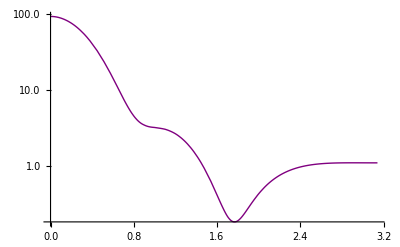

```mathematica
eik3p1=LogPlot[eik3interp1[θ],{θ,0,Pi},PlotStyle->Purple]
```

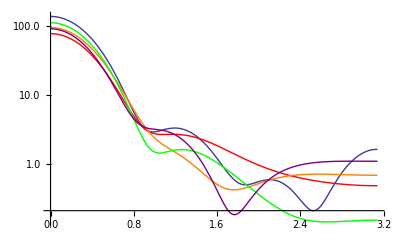

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,eik3p1,PlotRange->Automatic]
```

### Eikonal to third order for k = 1, 2, 3

```mathematica
eik1dσdΩ[2]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,293.229},{0.1,253.737},{0.2,163.545},{0.3,77.1219},{0.4,25.8275},{0.5,6.47019},{0.6,2.40483},{0.7,1.97084},{0.8,1.44185},{0.9,0.772509},{1.,0.346935},{1.1,0.179203},{1.2,0.127405},{1.3,0.0983604},{1.4,0.0691364},{1.5,0.0442011},{1.6,0.0277238},{1.7,0.01859},{1.8,0.0137187},{1.9,0.010736},{2.,0.00851045},{2.1,0.00669704},{2.2,0.00524199},{2.3,0.00413013},{2.4,0.00331794},{2.5,0.00274219},{2.6,0.00234029},{2.7,0.00206183},{2.8,0.00187093},{2.9,0.00174416},{3.,0.00166718},{3.1,0.001632}}

```mathematica
eik1interp2=Interpolation[%];
```

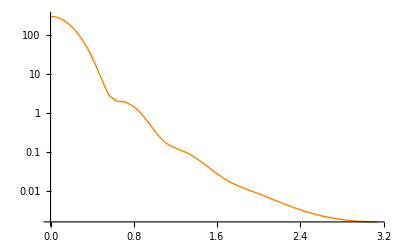

```mathematica
eik1p2=LogPlot[eik1interp2[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[2]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,294.891},{0.1,254.649},{0.2,163.044},{0.3,75.9351},{0.4,24.9955},{0.5,6.30489},{0.6,2.57006},{0.7,2.09458},{0.8,1.42198},{0.9,0.684686},{1.,0.273226},{1.1,0.143963},{1.2,0.117926},{1.3,0.0974434},{1.4,0.0684081},{1.5,0.0426767},{1.6,0.0269085},{1.7,0.0195534},{1.8,0.0164681},{1.9,0.0146459},{2.,0.0128563},{2.1,0.0109482},{2.2,0.00912235},{2.3,0.00756008},{2.4,0.00632944},{2.5,0.00541192},{2.6,0.00475075},{2.7,0.00428453},{2.8,0.00396253},{2.9,0.00374836},{3.,0.00361844},{3.1,0.00355914}}

```mathematica
eik2interp2=Interpolation[%];
```

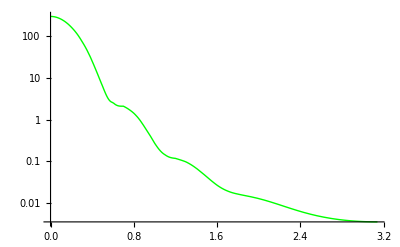

```mathematica
eik2p2=LogPlot[eik2interp2[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[2]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,294.867},{0.1,254.726},{0.2,163.303},{0.3,76.2613},{0.4,25.2329},{0.5,6.39604},{0.6,2.55184},{0.7,2.03178},{0.8,1.36394},{0.9,0.65195},{1.,0.261367},{1.1,0.138152},{1.2,0.107907},{1.3,0.08268},{1.4,0.0537613},{1.5,0.0322565},{1.6,0.0215244},{1.7,0.0176819},{1.8,0.0161767},{1.9,0.0147172},{2.,0.0129065},{2.1,0.0110678},{2.2,0.00951451},{2.3,0.00835394},{2.4,0.00754412},{2.5,0.00699088},{2.6,0.00660726},{2.7,0.00633332},{2.8,0.0061345},{2.9,0.00599355},{3.,0.005903},{3.1,0.00586009}}

```mathematica
eik3interp2=Interpolation[%];
```

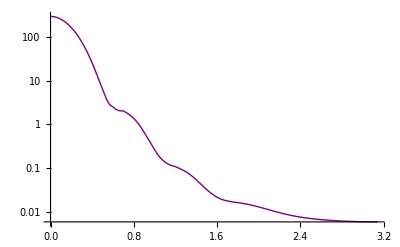

```mathematica
eik3p2=LogPlot[eik3interp2[θ],{θ,0,Pi},PlotStyle->Purple]
```

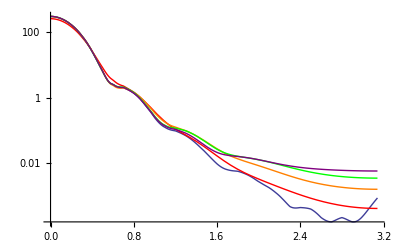

```mathematica
Show[p2,eik0p2,eik1p2,eik2p2,eik3p2]
```

```mathematica
eik1dσdΩ[3]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,374.138},{0.1,274.827},{0.2,105.998},{0.3,19.2216},{0.4,1.99512},{0.5,1.22341},{0.6,0.57887},{0.7,0.123655},{0.8,0.0445765},{0.9,0.0301565},{1.,0.0119942},{1.1,0.00370552},{1.2,0.00199877},{1.3,0.00125574},{1.4,0.000587395},{1.5,0.000244121},{1.6,0.000131493},{1.7,0.0000869334},{1.8,0.000053933},{1.9,0.000030146},{2.,0.0000167752},{2.1,0.0000103918},{2.2,7.26747×10^-6},{2.3,5.39165×10^-6},{2.4,4.05011×10^-6},{2.5,3.05423×10^-6},{2.6,2.3388×10^-6},{2.7,1.84691×10^-6},{2.8,1.52175×10^-6},{2.9,1.31618×10^-6},{3.,1.19699×10^-6},{3.1,1.1442×10^-6}}

```mathematica
eik1interp3=Interpolation[%];
```

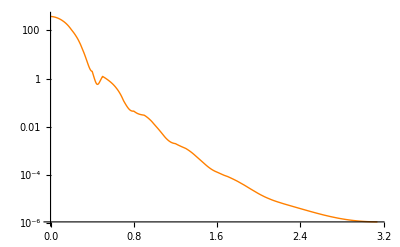

```mathematica
eik1p3=LogPlot[eik1interp3[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[3]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,373.822},{0.1,274.315},{0.2,105.467},{0.3,19.0624},{0.4,2.02441},{0.5,1.2095},{0.6,0.543894},{0.7,0.111024},{0.8,0.0428305},{0.9,0.0281936},{1.,0.0103956},{1.1,0.00335534},{1.2,0.00213821},{1.3,0.00135794},{1.4,0.00062945},{1.5,0.000292072},{1.6,0.000190363},{1.7,0.000137848},{1.8,0.0000888745},{1.9,0.0000524075},{2.,0.0000320027},{2.1,0.0000221226},{2.2,0.0000168856},{2.3,0.0000132998},{2.4,0.0000104517},{2.5,8.19866×10^-6},{2.6,6.51226×10^-6},{2.7,5.31722×10^-6},{2.8,4.5083×10^-6},{2.9,3.98736×10^-6},{3.,3.68128×10^-6},{3.1,3.54466×10^-6}}

```mathematica
eik2interp3=Interpolation[%];
```

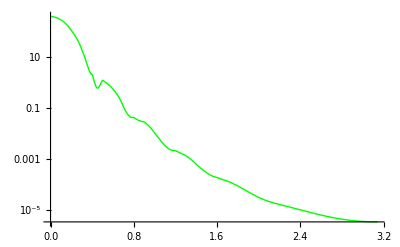

```mathematica
eik2p3=LogPlot[eik2interp3[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[3]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,373.882},{0.1,274.408},{0.2,105.556},{0.3,19.0824},{0.4,2.01275},{0.5,1.2013},{0.6,0.539485},{0.7,0.108083},{0.8,0.0404853},{0.9,0.026123},{1.,0.00913545},{1.1,0.00281383},{1.2,0.00181942},{1.3,0.00110967},{1.4,0.000497961},{1.5,0.000256272},{1.6,0.000188055},{1.7,0.000138832},{1.8,0.0000918617},{1.9,0.0000600539},{2.,0.0000428103},{2.1,0.0000332308},{2.2,0.0000266661},{2.3,0.0000214836},{2.4,0.0000173677},{2.5,0.0000142355},{2.6,0.0000119462},{2.7,0.0000103198},{2.8,9.19329×10^-6},{2.9,8.44371×10^-6},{3.,7.98935×10^-6},{3.1,7.78217×10^-6}}

```mathematica
eik3interp3=Interpolation[%];
```

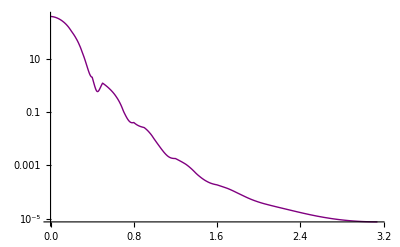

```mathematica
eik3p3=LogPlot[eik3interp3[θ],{θ,0,Pi},PlotStyle->Purple]
```

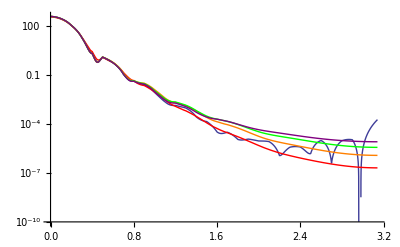

```mathematica
Show[p3,eik0p3,eik1p3,eik2p3,eik3p3]
```